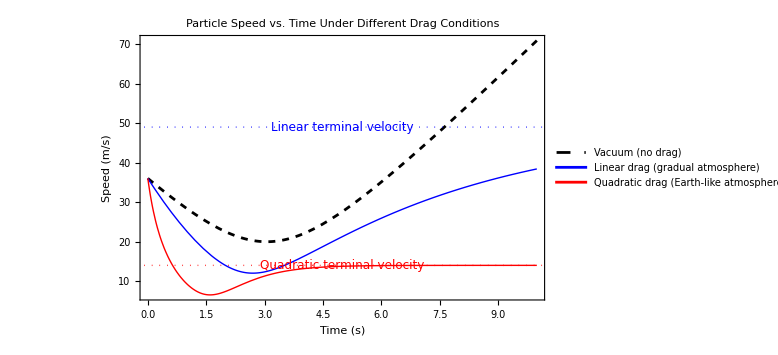
{{-Graphics-},{□},{□}}

```mathematica
(*This Wolfram Language (Mathematica) notebook is based on Classical Mechanics of the Physics course at UNESP Bauru.
It compares the velocity vs. time behavior of a particle moving under gravity in:
  1. Vacuum (no air resistance) 
2. Gradual atmosphere (linear drag,F_drag=-k*v) 
3. Earth-like atmosphere (quadratic drag,F_drag=-c*v^2)*)
ClearAll["Global`*"];

(* ======================*)
(*PHYSICAL PARAMETERS*)
(* ======================*)
m=1;          (*Mass of particle[kg]*)
g=9.81;       (*Acceleration due to gravity[m/s^2]*)
v0x=20;       (*Initial horizontal velocity[m/s]*)
v0y=30;       (*Initial vertical velocity[m/s]*)
k=0.2;        (*Linear drag coefficient[kg/s]*)
c=0.05;       (*Quadratic drag coefficient[kg/m]*)

(*Time range for simulation*)
tmax=10;      (*Maximum time[s]*)

(* ======================*)
(*VACUUM CASE*)
(* ======================*)
(*In vacuum,only gravity acts on the particle*)
vxVacuum[t_]:=v0x;  (*Horizontal velocity remains constant*)
vyVacuum[t_]:=v0y-g*t;  (*Vertical velocity changes linearly*)
speedVacuum[t_]:=Sqrt[vxVacuum[t]^2+vyVacuum[t]^2];

(* ======================*)
(*LINEAR DRAG CASE*)
(* ======================*)
(*Solution to m dv/dt=-k v-m g*)
vxLinear[t_]:=v0x*Exp[-(k/m)*t];
vyLinear[t_]:=(v0y+(m*g)/k)*Exp[-(k/m)*t]-(m*g)/k;
speedLinear[t_]:=Sqrt[vxLinear[t]^2+vyLinear[t]^2];

(*Terminal velocity for linear case*)
vTerminalLinear=m*g/k;

(* ======================*)
(*QUADRATIC DRAG CASE*)
(* ======================*)
(*Numerical solution required for quadratic drag*)
solutionQuadratic=NDSolve[{m*vx'[t]==-c*Sqrt[vx[t]^2+vy[t]^2]*vx[t],m*vy'[t]==-m*g-c*Sqrt[vx[t]^2+vy[t]^2]*vy[t],vx[0]==v0x,vy[0]==v0y},{vx,vy},{t,0,tmax}];

(*Extract the numerical functions*)
vxQuadratic[t_]:=vx[t]/. solutionQuadratic[[1]];
vyQuadratic[t_]:=vy[t]/. solutionQuadratic[[1]];
speedQuadratic[t_]:=Sqrt[vxQuadratic[t]^2+vyQuadratic[t]^2];

(*Terminal velocity for quadratic case*)
vTerminalQuadratic=Sqrt[m*g/c];

(* ======================*)
(*PLOT ALL CASES*)
(* ======================*)
{{Plot[{speedVacuum[t],speedLinear[t],speedQuadratic[t]},{t,0,tmax},PlotStyle->{{Black,Dashed},(*Vacuum*){Blue,Thick},(*Linear drag*){Red,Thick}        (*Quadratic drag*)},PlotLegends->{"Vacuum (no drag)","Linear drag (gradual atmosphere)","Quadratic drag (Earth-like atmosphere)"},Frame->True,FrameLabel->{Style["Time (s)",14,Bold],Style["Speed (m/s)",14,Bold]},PlotLabel->Style["Particle Speed vs. Time Under Different Drag Conditions",16,Bold],ImageSize->Large,PlotRange->All,Epilog->{(*Add terminal velocity markers*){Dotted,Blue,InfiniteLine[{{0,vTerminalLinear},{tmax,vTerminalLinear}}]},Text[Style["Linear terminal velocity",Blue,12],{tmax/2,vTerminalLinear},{0,-1.5}],{Dotted,Red,InfiniteLine[{{0,vTerminalQuadratic},{tmax,vTerminalQuadratic}}]},Text[Style["Quadratic terminal velocity",Red,12],{tmax/2,vTerminalQuadratic},{0,-1.5}]}]}, {□}, {□}}
```